# Name:

Show an appropriate amount of work.  You can (and probably should) check your work with a computer.

Compute and simplify a bit all possible values of

z=(ⅈ/(1+ⅈ))^3=

Roots of z^5=-32 ⅈ  
z=

Roots of (z-ⅈ)(z^2-4 ⅈ z+5)=0     
 z=

Sketch and label the sets

Points C_1 satisfying |z+ⅈ|<2.

Points C_2 satisfying re(z-ⅈ)=1.

Points C_3 satisfying arg(z+ⅈ)=3π/4.

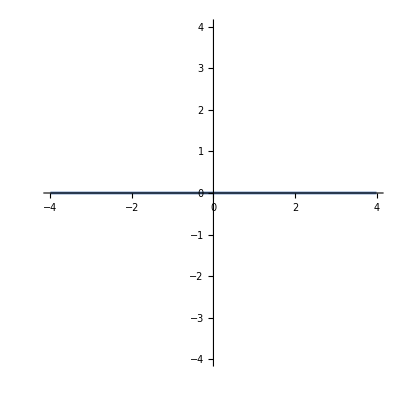

For f(z)=u(x,y)+ⅈ v(x,y) and write down the CR equations
                                                  and

Explain why u satisfies u_xx+u_yy=0.

Is ⅈ x^3-3 x^2 y-3 ⅈ x y^2+y^3 analytic? If it is write down f(z).

Is ⅈ x^3+3 x^2 y-3 ⅈ x y^2+y^3 analytic? If it is write down f(z).

Is ⅇ^(x-ⅈ y) analytic?                                               .

Explain steps and show appropriate work.

Compute∫_O ⅇ^(1/z) dz for the ccw unit circle. #5.6.1 p166

Compute ∫_0^∞ dx/(x^4+2 x^2 cos(2α)+1) 	#5.6.4 p166
As extra credit if you want to practice trig identities show it equals |π/(4 cos(α))|

Extra credit. Show ∫_0^∞ (ⅇ^-x-cos(x) dx)/x=0  			#5.6.5 p166

Compute ∫_(-∞)^∞ dx/(1+x^(2p)) 		#5.6.7 p166
As extra credit if you want to practice trig identities show it equals |π/(p sin(π/(2p)))|

Reminder d/dz(arcsin(z))=1/(√(1-z^2))

Discuss the singularities of f(z)=arcsin(z) for z∈ℂ

Compute two non-zero terms of the Taylor Series for f(z) about z=0.

Compute the general term of the Taylor Series for f(z) about z=0.

What is the radius of convergence for the TS about z=0?

What would be the radius of convergence for the TS about z=ⅈ?

f(z)=∑_(n=-∞)^(n=∞) a_n z^n is the Laurent Series for f about z=0.

What is the name for a_-1?  Why is it particularly important?

Write down a simple formula for a_n with n≥0 valid when f is analytic near z=0.

Write down a formula for a_n valid when f is not analytic near z=0.  Explain when this formula is valid.

Compute lim_(n→∞) ∑_(k=-n)^(k=n) 1/(n^4+1)using a contour integral. Explain your steps and show appropriate work.  In this problem you do not need to compute residues. If you have defined f and z_i you can just write res(f,z_i) for the residue.

For the closed counter clockwise contour Γ shown below 
p_1(t)=                                                              for 0≤t<1
p_2(t)=                                                              for 0≤t<1
∫_Γ f(z)dz=∫_0^1                                           dt+∫_0^1                                           dt.
For f(z)=z^2/(z-ⅈ) evaluate ∫_Γ f(z)dz=                                              .  Show appropriate work below.

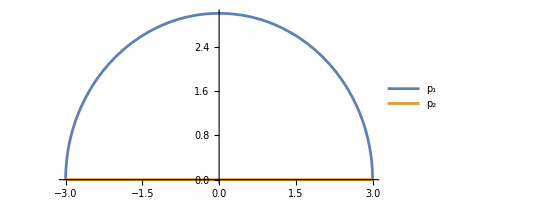

```mathematica
p1[t_]:=3 E^(π ⅈ t)
p2[t_]:=-3+6 t
ParametricPlot[{ReIm[p1[t]],ReIm[p2[t]]},{t,0,1},PlotLegends->{"p_1","p_2"}]
```

For the closed counter clockwise contour Γ shown below
 
p_1(t)=                                                              for 0≤t<1
p_2(t)=                                                              for 0≤t<1
p_3(t)=                                                              for 0≤t<1 
∫_Γ f(z)dz=∫_0^1                                           dt+∫_0^1                                           dt+∫_0^1                                           dt
For f(z)=ⅈ/(z-(1+2ⅈ)) evaluate ∫_Γ f(z)dz=                                                  .  
Explain the need for care when evaluating these individual line integrals using FTC and logs.

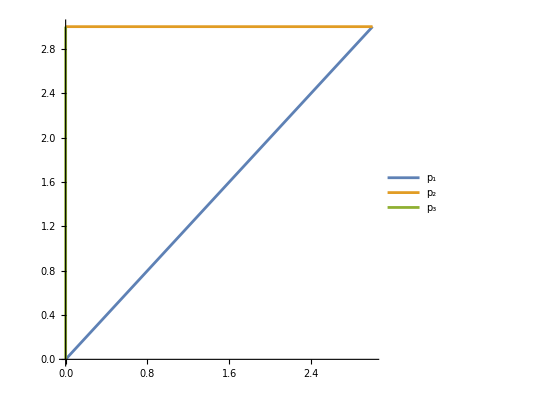

```mathematica
p1[t_]:=(3+3 ⅈ)t
p2[t_]:=3+3ⅈ -3 t
p3[t_]:= 3 ⅈ - 3 ⅈ t
ParametricPlot[{ReIm[p1[t]],ReIm[p2[t]],ReIm[p3[t]]},{t,0,1},PlotLegends->{"p_1","p_2","p_3"}]
```

Compute ∫_Γ ⅇ^z/((z^2+9)(z-3))dz=                                                             for the counter clockwise contour Γ. Show appropriate work.

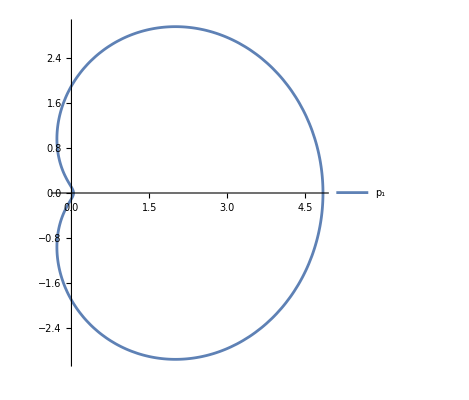

```mathematica
p1[t_]:=(E^(2π ⅈ t)+1.2)^2
ParametricPlot[ReIm[p1[t]],{t,0,1},PlotLegends->{"Γ"}]
```